```mathematica
s="D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\D_L500OT200000_u12t100.txt";
data=ReadList[s,{Number,Number}];
f=Fit[data,{1,x},x]
Show[ListPlot[data,Frame->True,FrameLabel->{Style["t",24],Style["<r^2>_particles",24]}],Plot[f,{x,0,10^7},PlotStyle->Red,PlotLegends->{"0.364±0.005"}]]
Position[data,{_,1.}]
Length[data]
```

30.6185+0.118002 x

7

{0.0635743,0.00347876}

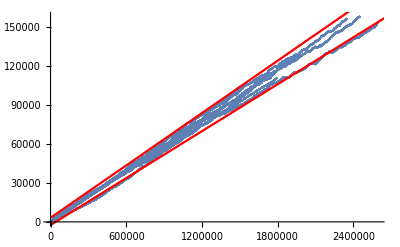

```mathematica
data=ReadList[s,{Number,Number}];
g=Block[
{
startList=Position[data,{_,1.}],
prepData
},
startList=Table[{startList[[i,1]],startList[[i+1,1]]-1},{i,Length@startList-1}]~Join~{{startList[[-1,1]],Length@data}};
prepData=Map[Take[data,#]&,startList];
Map[LinearModelFit[#,{1,x},x]["BestFitParameters"]&,prepData]
];
Length[g]
{Mean[g][[2]],StandardDeviation[g][[2]]}
Show[ListPlot[data],Plot[{Mean[g]+StandardDeviation[g],Mean[g]-StandardDeviation[g]}.({{1}, {x}}),{x,0,10000000},PlotStyle->Red]]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.0623303 | 0.0119991 | {0.0365949,0.0880657}
x | 1.11584 | 0.00652431 | {1.10185,1.12983}

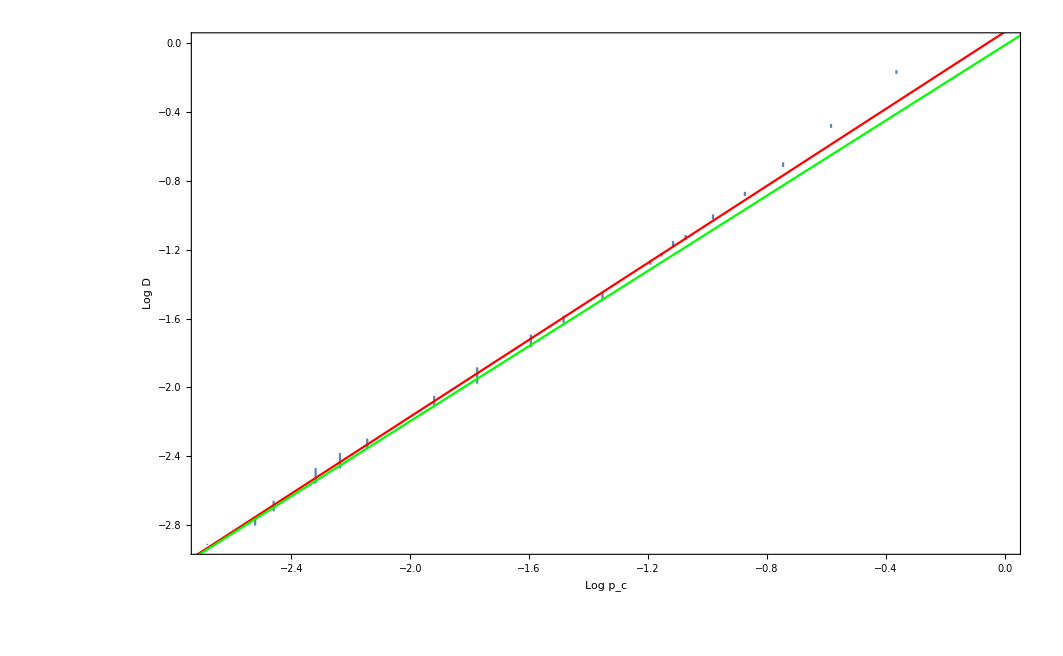

```mathematica
Needs["ErrorBarPlots`"];
prepdata={{2,0.8442824179807262,0.008946764718241804},{4,0.6174504081642859,0.00654155730957181},{6,0.493073051223044,0.006562599439543041},{8,0.4161871691379425,0.005027812128851078},{10,0.3642464874279804,0.00525335590572019},{12,0.3232289237629086,0.004518678803052814},{13,0.311520052089516,0.004692801718656046},{14,0.29249323231782576,0.0030611198670020723},{15,0.2791588045845123,0.003212583075302566},{20,0.23045600974828812,0.00449574135650338},{25,0.20106746114895677,0.004109020976421343},{30,0.17728186061944823,0.006593451850948006},{40,0.14507739909337658,0.0068763812097285834},{50,0.12524047059171914,0.0035068661683741336},{70,0.09769061021742578,0.002877924715932662},{80,0.08846765744274393,0.003936758641868083},{90,0.08112432719348138,0.003534829100430593},{110,0.06800344013093632,0.0020819874437532997},{120,0.06236867874144046,0.0016876078841425882},{150,0.054476955747954116,0.00014540352568524967}};
errordata=Table[{{Log[3.82/prepdata[[i,1]] ProductLog[prepdata[[i,1]]/3.82]],Log[prepdata⟦i,2⟧]},ErrorBar[0,prepdata⟦i,3⟧/prepdata⟦i,2⟧]},{i,1,Length[prepdata]}];
fitdata=Table[{errordata[[i,1,1]],errordata[[i,1,2]]},{i,5,Length[prepdata]}];
f=LinearModelFit[fitdata,{1,x},x];
f["ParameterConfidenceIntervalTable"]
Show[ErrorListPlot[errordata,PlotStyle->PointSize[.00],Frame->True,FrameLabel->{"Log p_c","Log D"}],Plot[{f[x],1.09(x+1.5)-1.65},{x,-5,5},PlotStyle->{Red,Green}]]
```

FittedModel[-0.190411+1.12182 x]

| Estimate | Standard Error | Confidence Interval
1 | -0.190411 | 0.0382797 | {-0.273816,-0.107007}
x | 1.12182 | 0.0179617 | {1.08269,1.16096}

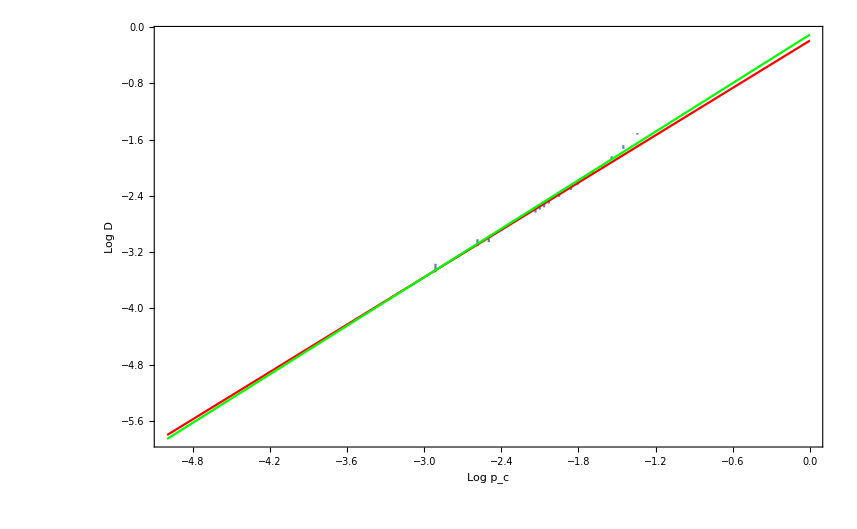

```mathematica
Needs["ErrorBarPlots`"];
prepdata100={{2,0.2194839898025424,0.0025330025242705184},{4,0.18193602648008267,0.004753601892745142},{6,0.15625349273030023,0.0032173094432827545},{8,0.13866468772538867,0.0015182206061401208},{10,0.12771510738513428,0.0020168274302741814},{12,0.11732566253640227,0.0024396322788896078},{14,0.10897641985192741,0.002824041526603051},{16,0.10200077909544362,0.0030653002857002824},{20,0.0910029472919453,0.001529588164953236},{24,0.08396280478527807,0.0024852430531449345},{26,0.07952233438816396,0.00245291014902176},{28,0.07675482294670104,0.0021109183643393038},{30,0.07381192393818596,0.0022904842235867812},{50,0.056508780703200354,0.0010095578783326656},{60,0.04822125644909938,0.0012296876943978222},{70,0.04665396201468282,0.002287574420784968},{120,0.032565665692149026,0.0019720884183409048}};
errordata100=Table[{{Log[3.82/prepdata100[[i,1]] ProductLog[prepdata100[[i,1]]/3.82(1/100)^(1/3.82)]],Log[prepdata100[[i,2]]]},ErrorBar[0,prepdata100[[i,3]]/prepdata100[[i,2]]]},{i,1,Length[prepdata100]}];
fitdata100=Table[{errordata100[[i,1,1]],errordata100[[i,1,2]]},{i,4,Length[prepdata100]}];
f100=LinearModelFit[fitdata100,{1,x},x]
f100["ParameterConfidenceIntervalTable"]
Show[ErrorListPlot[errordata100,PlotStyle->PointSize[.000],Frame->True,FrameLabel->{"Log p_c","Log D"},PlotRange->{-1.4,-3.6}],Plot[{f100[x],1.15(x+2.3)-2.75},{x,-5,0},PlotStyle->{Red,Green}]]
```

```mathematica
(2*1.33-0.140+1.30)/1.30
```

2.93846

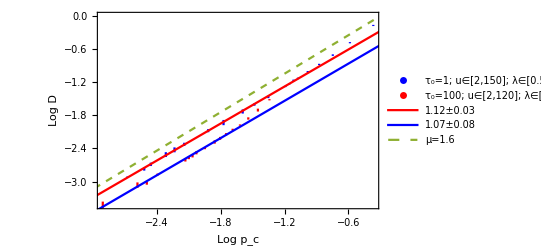

```mathematica
Show[Legended[ErrorListPlot[{errordata,errordata100},PlotStyle->{{PointSize[.000],Blue},{PointSize[.000],Red}},Frame->True,FrameLabel->{"Log p_c","Log D"},PlotRange->All],PointLegend[{Blue, Red},{"τ_0=1; u∈[2,150]; λ∈[0.5,30]; p_p=-0.98; λ_p = 2.6","τ_0=100; u∈[2,120]; λ∈[0.15,10]; p_p=-1.62; λ_p = 0.6"}]],Plot[{Legended[f[x],"1.12±0.03"],Legended[f100[x],"1.07±0.08"],Legended[1.16(x+0.3),"μ=1.6"]},{x,-5,0},PlotStyle->{Red, Blue, Dashed}]]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.665009 | 0.030178 | {0.599257,0.730761}
x | -0.709372 | 0.00782339 | {-0.726418,-0.692326}

FittedModel[-0.808366-0.534951 x]

| Estimate | Standard Error | Confidence Interval
1 | -0.808366 | 0.0358935 | {-0.886571,-0.73016}
x | -0.534951 | 0.0107578 | {-0.55839,-0.511511}

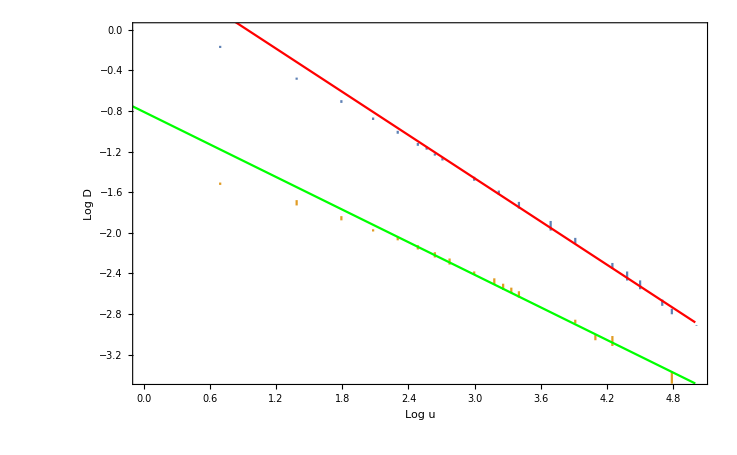

```mathematica
errordata=Table[{{Log[prepdata[[i,1]]],Log[prepdata⟦i,2⟧]},ErrorBar[0,prepdata⟦i,3⟧/prepdata⟦i,2⟧]},{i,1,Length[prepdata]}];
errordata100=Table[{{Log[prepdata100[[i,1]]],Log[prepdata100[[i,2]]]},ErrorBar[0,prepdata100[[i,3]]/prepdata100[[i,2]]]},{i,1,Length[prepdata100]}];
fitdata=Table[{errordata[[i,1,1]],errordata[[i,1,2]]},{i,7,Length[prepdata]}];
fitdata100=Table[{errordata100[[i,1,1]],errordata100[[i,1,2]]},{i,4,Length[prepdata100]}];
f=LinearModelFit[fitdata,{1,x},x];
f["ParameterConfidenceIntervalTable"]
f100=LinearModelFit[fitdata100,{1,x},x]
f100["ParameterConfidenceIntervalTable"]
Show[ErrorListPlot[{errordata,errordata100},PlotStyle->PointSize[.00],Frame->True,FrameLabel->{"Log u","Log D"}],Plot[{f[x],f100[x]},{x,-5,5},PlotStyle->{Red,Green}]]
```